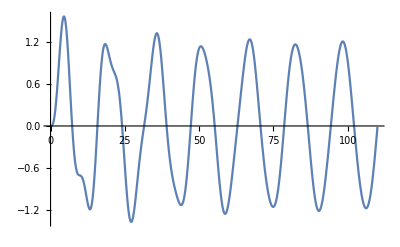

```mathematica
ClearAll["Global`*"]
(*We will begin with analytical solution of mass spring system *)
t0=0;tf=110;
m=1;
ωn=1;  ζ=0.03;
F0=1;
ω=0.4;
(*Initial condition of mass spring system *)
(*x[0]==0      ,x'[0]==0*)
x0=0;
v0=0;
(*---------------------------------------*)
ωd=√(1-ζ^2) ωn;
A=(F0 ω ((2 ζ^2-1) ωn^2+ω^2))/(m ωd ((2 ζ ω ωn)^2+(ωn^2-ω^2)^2))+v0/ωd+(ζ x0 ωn)/ωd;
B=(2 ζ F0 ω ωn)/(m ((2 ζ ω ωn)^2+(ωn^2-ω^2)^2))+x0;
x[t_]=ⅇ^(-ζ t ωn) (A Sin[t ωd]+B Cos[t ωd])+(F0/(m ((2 ζ ω ωn)^2+(ωn^2-ω^2)^2))) ((ωn^2-ω^2) Sin[t ω]-2 ζ ω ωn Cos[t ω]);
Plot[x[t],{t,t0,tf}]
```

```mathematica
(*Comparsion between analytical solution and solving Runge kutta method *)
n=100;
t=Table[j,{j,1,n+1}];
y1=Table[j,{j,1,n+1}];
y2=Table[j,{j,1,n+1}];
(* Initial conditions *)
t[[1]]=t0;
y1[[1]]=x0;
y2[[1]]=v0 ;
f1[t_,y1_,y2_]:=y2
f2[t_,y1_,y2_]:=-2 ζ ωn y2-ωn^2  y1 +F0 Sin[ω t]/m;
h=(tf-t0)/n;
For[i=1,i<n+1,i++,
{
k1=f1[t[[i]],y1[[i]],y2[[i]]];
m1=f2[t[[i]],y1[[i]],y2[[i]]];
k2=f1[t[[i]]+h/2,y1[[i]]+h k1/2,y2[[i]]+h m1/2];
m2=f2[t[[i]]+h/2,y1[[i]]+h k1/2,y2[[i]]+h m1/2];
k3=f1[t[[i]]+h/2,y1[[i]]+h k2/2,y2[[i]]+h m2/2];
m3=f2[t[[i]]+h/2,y1[[i]]+h k2/2,y2[[i]]+h m2/2];
k4=f1[t[[i]]+h,y1[[i]]+h k3,y2[[i]]+h m3];
m4=f2[t[[i]]+h,y1[[i]]+h k3,y2[[i]]+h m3];
(*Find iteration solution *)
t[[i+1]]=t[[i]]+h;
y1[[i+1]]=y1[[i]]+h/6(k1+2k2+2k3+k4);
y2[[i+1]]=y2[[i]]+h/6(m1+2 m2+2 m3+m4);
}]
```

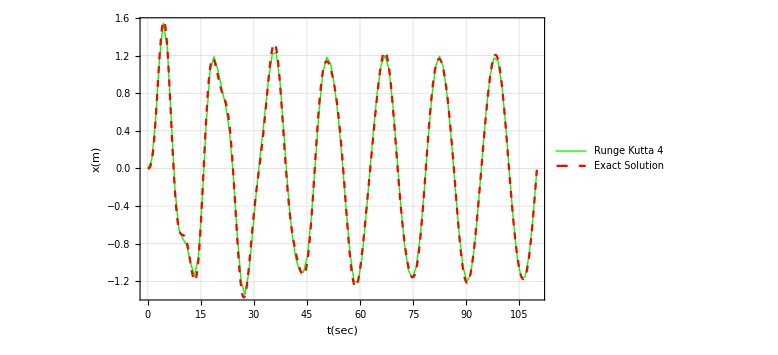

```mathematica
data=Table[{t[[j]],y1[[j]]},{j,1,n+1}];
fig1=ListLinePlot[data,Frame-> True,PlotRange->All,PlotStyle->Green,
FrameLabel->{"t(sec)","x(m)"},GridLines->None,PlotTheme->"Classic",
ImageSize->Large,PlotLegends->{Framed["Runge Kutta 4"]}];
fig2=Plot[x[c],{c,t0,tf},PlotStyle->{Dashed,Red},
PlotLegends->{Framed["Exact Solution"]}];
Show[{fig1,fig2},GridLines->Automatic,GridLinesStyle->LightGray]
```